```mathematica
g=9.8; (*grav. constant*)
m=6; (*Kilograms*)
vt=35;(*Terminal velocity*)
v=30;(*m/s*)

θ=50*π/180; (*50 degrees*)

ode1={x''[t]==(-g*x'[t]/vt^2)*√((x'[t])^2+(y'[t])^2),y''[t]==-g*(1+y'[t]/vt^2)*√((x'[t])^2+(y'[t])^2),x[0]==0,x'[0]==v*Cos[θ],y[0]==2,y'[0]==v*Sin[θ]};
sol=NDSolve[ode1,{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

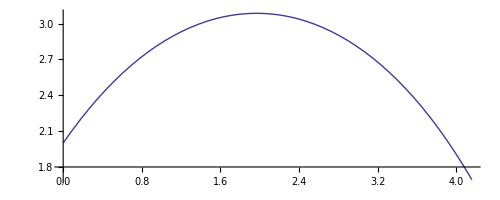

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,.22}]
```

```mathematica
(*Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]*)
```